```mathematica
ClearAll["Global`*"] (*clear all variables to avoid errors*)
NotebookSave[]
Drop[DateList[],{1,3}](*Hour when the computation started*)
Get["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Functions\\Function_Garch.m"];
(*get function "Simul" written on file Function_Garch.nb. This function does exactly the same as the whole file Simulation_Garch.nb, only it does it as a single function with a single return that corresponds to the option price.*)
(*This function expects the inputs - Simul[M,callput,n,T,K,r,sigma,S0,a,b,w] (see below)*)
```

{19,49,45.9053044}

Set Parameters

```mathematica
Num=500; (*Number of simulations per vector - See the article by Sobol for more information*)
M=50000; (*Number of paths to be generated on each simulation*)
callput="Put"; (*Type of option - "Call" or "Put"*)
n=12.; (*Number of exercise chances per year*)
T=1.; (*Number of years until exercise*)
k=40.; (*Strike price*)
Exporting=False; (*Choose True if you want the final matrices and images to be exported. Choose False otherwise. If you want to export the results, change the paths at the end of the file to the appropriate destination.*)

(*It should be noted that a total number of "Num*(number of random input variabes + 2)", or, in this case, Num*5 instances of the simulation will have to be performed. This means that a large value of Num will result in a very long computation time*)


(*The volatility is updated using the GARCH(1,1) model. The following equation is used:*)
(*sigma_(i+1)^2 = a * ((S_(i+1)-S_i)/(S_i)) + b * sigma_i^2 + w*)
(*"a" indicates the influence of the price change in the volatility. "b" indicates the influence of the previous volatility on the future volatility. "w" is related to the influence of the long-term volatility*)
a=0.05;
b=0.9;
w=0.3;
```

Distribution Parameters

```mathematica
(*we assume the variables for the interest rate (r), stock price volatility (σ) and initial stock price (S0) follow a normal distribution. This particular choice of variables was arbitrary.*)
(*The final output of the sensitivity analysis, Vi, for each of these variables, will indicate what fraction of price variance is generated by the individual variance of the respective input.*)
rm=0.06; (*interest rate expected value*)
rs=0.001; (*interest rate standard deviation*)
sigmam=0.2; (*stock price volatility expected value*)
sigmas=0.01;(*stock price volatility standard deviation*)
S0m=44.; (*initial stock price expected value*)
S0s=.1;(*initial stock price standard deviation*)
```

Sensitivity Analysis

```mathematica
distrib={rdist,sigmadist,S0dist}={NormalDistribution[rm,rs],NormalDistribution[sigmam,sigmas],NormalDistribution[S0m,S0s]};(*Vector with the distributions of each input variable.*)
```

```mathematica
matrix=Table[distrib,{i,1,Num}];(*Table with distributions*)
```

```mathematica
MatRand1=Map[RandomVariate,matrix,{2}];(*Matrix with the randomized inputs to be used on vector A.*)
MatRand2=Map[RandomVariate,matrix,{2}];(*Matrix with the randomized inputs to be used on vector B*)
```

```mathematica
Param=Table[{M,callput,n,T,k},{i,1,Num}];(*Matrix with non-random input parameters*)
```

```mathematica
MatA=Join[Param,MatRand1,2];(*Matrix with input parameters (non-random + random) to be used on vector A. Each row contains the set of parameters needed to obtain the option price.*)
MatB=Join[Param,MatRand2,2];(*Matrix with input parameters (non-random + random) to be used on vector B*)
```

```mathematica
For[i=Dimensions[Param][[2]]+1;VMat={},i≤Dimensions[MatA][[2]],i++,tmp=MatB;tmp[[All,i]]=MatA[[All,i]];AppendTo[VMat,tmp]] (*Generation of input parameter matrices VMat[[i]]. They are similar to matrix MatB, with the i^th column replaced by the i^th column of matrix MatA*)
```

```mathematica
fA=ParallelTable[Simul@@MatA[[it3]],{it3,1,Num}];//AbsoluteTiming(*Vector A generation. We use the input matrix MatA and calculate the option price using all the input parameters on each row*)
```

{0.828399,Null}

```mathematica
fB=ParallelTable[Simul@@MatB[[it4]],{it4,1,Num}];(*Vector B generation.*)
```

```mathematica
Monitor[For[it2=1;fVA={},it2<=Dimensions[VMat][[1]],it2++,tmp=ParallelTable[Simul@@VMat[[it2,it1]],{it1,1,Num}];AppendTo[fVA,tmp]],ProgressIndicator[it2,{1,Dimensions[VMat][[1]]}]];(*Vectors fVA[[i]] generation. The inputs used were the matrices VMat[[i]].*)
```

```mathematica
For[x=1;Vi={},x≤Dimensions[fVA][[1]],x++,tmp=1/Num*Sum[fA[[w]]*(fVA[[x,w]]-fB[[w]]),{w,1,Num}];AppendTo[Vi,tmp]] ;Vi(*Contribution of each variable to the final variance. The output is (r,sigma,S0).*)
```

{-0.00782619,-0.00396712,0.00101174}

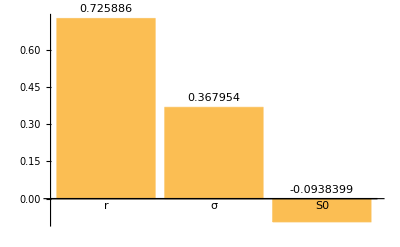

```mathematica
BarChart[Vi/Total[Vi,2],ChartLabels->{"r","σ","S0"},LabelingFunction->Above]
```

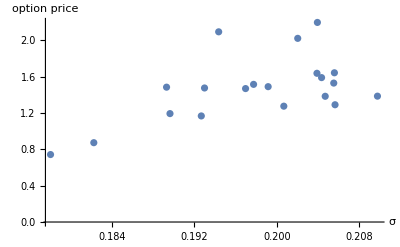

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,2]],MatRand2[[All,2]]]},{Join[fA,fB]},1]],AxesLabel->{"σ","option price"}]
```

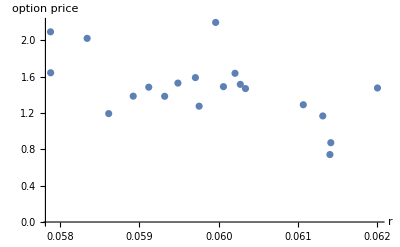

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,1]],MatRand2[[All,1]]]},{Join[fA,fB]},1]],AxesLabel->{"r","option price"}]
```

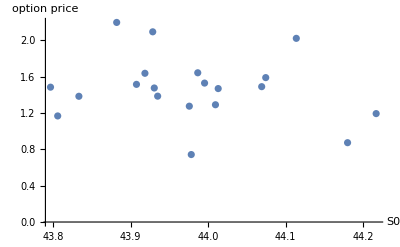

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,3]],MatRand2[[All,3]]]},{Join[fA,fB]},1]],AxesLabel->{"S0","option price"}]
```

```mathematica
(*If the variable Exporting was set to True, export the results. This might be useful to avoid repeating lengthy computations.*)
If[Exporting,Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\MatA5.m",MatA];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\MatB5.m",MatB];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fA5.m",fA];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fB5.m",fB];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fVA5.m",fVA];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\Param5.m",Param[[1]]],];
If[Exporting,Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\sigma5.eps",ListPlot[Transpose[Join[{Join[MatRand1[[All,2]],MatRand2[[All,2]]]},{Join[fA,fB]},1]],AxesLabel->{"σ","option price"}],"eps"];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\r5.eps",ListPlot[Transpose[Join[{Join[MatRand1[[All,1]],MatRand2[[All,1]]]},{Join[fA,fB]},1]],AxesLabel->{"r","option price"}]];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\S05.eps",ListPlot[Transpose[Join[{Join[MatRand1[[All,3]],MatRand2[[All,3]]]},{Join[fA,fB]},1]],AxesLabel->{"S0","option price"}],"eps"],];
```

```mathematica
NotebookSave[]
```